```mathematica
Series[2^s Pi^(s-1) Sin[Pi s/2]Gamma[1-s]Zeta[1-s],{s,0,1}]
```

-1/2+1/2 (-Log[2]-Log[π]) s+O[s]^2

```mathematica
D[1/n^s,s]
```

-n^-s Log[n]

```mathematica
D[1/(1+z zb)^2,z]
D[1/(1+z zb)^2,zb]
```

-(2 zb)/(1+z zb)^3

-(2 z)/(1+z zb)^3

```mathematica
D[ (2 zb)/(1+z zb),zb]+D[ (2 z)/(1+z zb),z]//Simplify
```

4/(1+z zb)^2

```mathematica
1+2*(Zeta[0])
```

0

```mathematica
Integrate[Exp[I m r Cos[θ]],{θ,0,2Pi}]
```

ConditionalExpression[2 π BesselJ[0,m r],m r∈ℝ]

```mathematica
Integrate[(p BesselJ[0,p r])/(p^2+m^2),{p,0,Infinity}]
```

ConditionalExpression[BesselK[0,r/(√(1/m^2))],Re[m]≠0&&((Re[r]==0&&Im[r]>0)||Re[r]>0)]

```mathematica
Series[2 π BesselI[0,m r],{m,0,4}]
```

2 π+1/2 π r^2 m^2+1/32 π r^4 m^4+O[m]^5

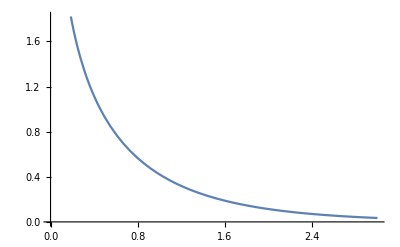

```mathematica
Plot[BesselK[0,m],{m,0,3}]
```

```mathematica
Assuming[r>0&&m>0,Integrate[p/(p^2+m^2)Cos[p r],{p,0,Infinity}]]
```

1/2 √π MeijerG[{{0},{}},{{0,0},{1/2}},(m^2 r^2)/4]

```mathematica
PolyGamma[0,1/2]//N
EulerGamma-Log[1/4]//N
```

-1.96351

1.96351

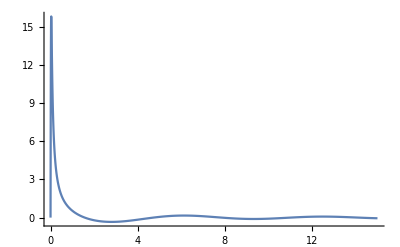

```mathematica
Plot[p/(p^2+0.001)Cos[p],{p,0,15},PlotRange->All]
```

```mathematica
D[p/(p^2+m^2),{p,1}]//Together
```

(m^2-p^2)/((m^2+p^2)^2)

```mathematica
p/(p^2+m^2)/.p->m
```

1/(2 m)

```mathematica
Assuming[m>0,Integrate[p/(p^2+m^2)Exp[-p^2 r^2],{p,0,Infinity}]]
```

ConditionalExpression[1/2 ⅇ^(m^2 r^2) Gamma[0,m^2 r^2],Re[r^2]≥0]

```mathematica
Series[1/2 ⅇ^(m^2 r^2) Gamma[0,m^2 r^2],{m,0,0}]
```

Floor[(π-2 Arg[m]-Arg[r^2])/(2 π)] (-ⅈ π+O[m]^1)+(1/2 (-EulerGamma-2 Log[m]-Log[r^2])+O[m]^1)

```mathematica
Series[Gamma[0,ϵ],{ϵ,0,0}]
```

(-EulerGamma-Log[ϵ])+O[ϵ]^1

```mathematica
D[z/(z zb+μ^2),z]//Together
```

μ^2/((z zb+μ^2)^2)

```mathematica
Integrate[r/((r^2+μ^2)^2),{r,0,Infinity}]
```

ConditionalExpression[1/(2 μ^2),Re[μ]≠0]

```mathematica
Assuming[r>0&&m>0,Integrate[p^2/(p^2+m^2)Exp[-p r],{p,0,Infinity},PrincipalValue->True]]
```

```mathematica
1/r-m CosIntegral[m r] Sin[m r]-1/2 m Cos[m r] (π-2 SinIntegral[m r])/.m->I m//Simplify
```

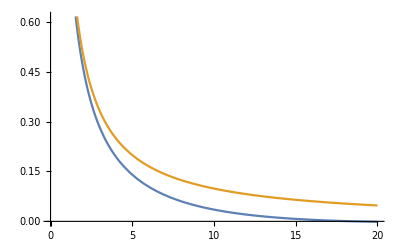

```mathematica
Plot[{Re[1/r-m CosIntegral[m r] Sin[m r]-1/2 m Cos[m r] (π-2 SinIntegral[m r])/.m->0.1 I],m  BesselK[1,m r]/.m->0.01},{r,0,20}]
```

```mathematica
Integrate[p^2/(p^2-m^2)Exp[-p r],{p,0,Infinity},PrincipalValue->True]
```

$Aborted

```mathematica
Integrate[(p Exp[-p r])/Sqrt[p^2-m^2],{p,m,Infinity}]
```

ConditionalExpression[m BesselK[1,m r],Re[m]>0&&Im[m]==0&&Re[r]>0]

```mathematica
Assuming[r>0&&m>0,Integrate[(p Exp[I p r])/(2 Sqrt[p^2+m^2]),{p,0,Infinity}]]
```

1/4 ⅈ (π BesselI[0,m r]-2 ⅈ BesselK[0,m r]-π StruveL[0,m r])

```mathematica
Assuming[m>0,Integrate[1/(2m)Exp[-1/2(p-m)^2/(2 m^3)]Exp[I p r],{p,-Infinity,Infinity}]]
```

ⅇ^(m r (ⅈ-m^2 r)) √m √π

```mathematica
D[p/(p^2+m^2),{p,2}]/.p->m
```

-1/(2 m^3)

```mathematica
Series[1/2 √π MeijerG[{{0},{}},{{0,0},{1/2}},(m^2 r^2)/4],{m,0,0}]
```

Floor[(π-2 Arg[m]-Arg[r^2])/(2 π)] (-ⅈ π+O[m]^1)+(1/2 (-EulerGamma-2 Log[m]-Log[r^2/4]+PolyGamma[0,1/2])+O[m]^1)

```mathematica
Series[-1/2 Cosh[m r] (CosIntegral[-ⅈ m r]+CosIntegral[ⅈ m r]-2 Log[r]+Log[r^2])+Sinh[m r] SinhIntegral[m r],{m,0,0}]
```

Floor[(π-Arg[m]-Arg[-ⅈ r])/(2 π)] (-ⅈ π+O[m]^1)+Floor[(π-Arg[m]-Arg[ⅈ r])/(2 π)] (-ⅈ π+O[m]^1)+(1/2 (-2 EulerGamma-2 Log[m]-Log[-ⅈ r]-Log[ⅈ r]+2 Log[r]-Log[r^2])+O[m]^1)

```mathematica
Series[1/2 Cosh[m r] (-2 CosIntegral[-ⅈ m r]+Log[1/m^2]+2 Log[m])-1/2 ⅈ √(1/m^2) m π Sinh[m r]+Sinh[m r] SinhIntegral[m r],{m,0,0}]
```

Floor[(π-Arg[m]-Arg[-ⅈ r])/(2 π)] (-2 ⅈ π+O[m]^1)+(1/2 (-2 EulerGamma+Log[1/m^2]-2 Log[-ⅈ r])+O[m]^1)

```mathematica
D[1/(x1-x2)^(Δ1+Δ2),x1]
```

(x1-x2)^(-1-Δ1-Δ2) (-Δ1-Δ2)

```mathematica
(x1-x2)^(-1-Δ1-Δ2) (-Δ1-Δ2)==
```

```mathematica
DSolve[x^2 f'[x]+b x f'[x]+(c x+d)f[x]==0,f,x]
```

{{f→Function[{x},ⅇ^(-(d Log[x])/b-((b c-d) Log[b+x])/b) C[1]]}}

```mathematica
Integrate[(Exp[u]+a)/(Exp[u]+b),u]
```

(a u+(-a+b) Log[b+ⅇ^u])/b

```mathematica
Integrate[(a Exp[u]-c)/(b-Exp[u]),u]
```

(-c u+(-a b+c) Log[b-ⅇ^u])/b

```mathematica
D[(x12 (x14-x13))/(x13(x14-x12)),x13]//Simplify
```

(x12 x14)/(x13^2 (x12-x14))

```mathematica
D[1/(z-w)^2,{w,3}]
```

24/(-w+z)^5

```mathematica
dXdX=-α/2 1/(z-w)^2;
T=-1/α (dX dX-dXdX)//Expand
T T//Expand
```

-1/(2 (-w+z)^2)-dX^2/α

1/(4 (-w+z)^4)+dX^4/α^2+dX^2/((-w+z)^2 α)

```mathematica
D[1/α dXdX,{w,2}]
```

-3/(-w+z)^4

```mathematica
2 1/α(dXdX)(D[dXdX,{w,2}])
```

(3 α)/(-w+z)^6

```mathematica
2 1/α dXdX*D[dXdX,{w,2}]//Expand
```

(3 α)/(-w+z)^6

```mathematica
(*(d^2X)^2*)
-1/α 2 D[dXdX,w]^2
-1/α 4 D[dXdX,w]
```

-(2 α)/(-w+z)^6

4/(-w+z)^3

```mathematica
-1/α 2 dXdX D[dXdX,{w,2}]
```

-(3 α)/(-w+z)^6

```mathematica
-2/α D[dXdX,{w,2}]
```

6/(-w+z)^4

```mathematica
Td4X
```

(24 dX[w])/(-w+z)^5+(24 dX'[w])/(-w+z)^4+(12 dX''[w])/(-w+z)^3+(4 dX^(3)[w])/(-w+z)^2+(dX^(4)[w])/(-w+z)

```mathematica
dXdX=-α/2 1/(z-w)^2;
TdX=dX[w]/(z-w)^2+dX'[w]/(z-w);
Td2X =(2 dX[w])/(-w+z)^3+(2 dX'[w])/(-w+z)^2+dX''[w]/(-w+z);
Td3X=(6 dX[w])/(-w+z)^4+(6 dX'[w])/(-w+z)^3+(3 dX''[w])/(-w+z)^2+(Derivative[3][dX][w])/(-w+z);
Td4X=(24 dX[w])/(-w+z)^5+(24 dX'[w])/(-w+z)^4+(12 dX''[w])/(-w+z)^3+(4 Derivative[3][dX][w])/(-w+z)^2+(Derivative[4][dX][w])/(-w+z);

TdX2=α/2 1/(z-w)^4+(2 dX[w]dX[w])/(z-w)^2+(2dX dX'[w])/(z-w);
TdX3=6 dX[w] TdX2+2/α(dX[w]+(w-z)dX'[w]) dXdX dX[w]^2//Expand;
TdX3=(3 α dX[w])/(-w+z)^4+(11 dX[w]^3)/(-w+z)^2+(12 dX dX[w] dX'[w])/(-w+z)+(dX[w]^2 dX'[w])/(-w+z)^2;
TdX4=6 dX[w]^2 TdX2+2/α(dX[w]+(w-z)dX'[w])dXdX dX[w]^3//Expand;
TdX4=-(3 α dX[w]^2)/(-w+z)^4+(11 dX[w]^4)/(-w+z)^2+(12 dX dX[w]^2 dX'[w])/(-w+z)+(dX[w]^3 dX'[w])/(-w+z);
TdXd2X=dX'[w]TdX+dX[w]Td2X+2 dXdX dX'[w]+D[dXdX,w]dX[w]//Expand
```

-(α dX[w])/(-w+z)^3+(2 dX[w]^2)/(-w+z)^3-(α dX'[w])/(-w+z)^2+(3 dX[w] dX'[w])/(-w+z)^2+dX'[w]^2/(-w+z)+(dX[w] dX''[w])/(-w+z)

```mathematica
Td3X
TdX3
TdXd2X
```

(6 dX[w])/(-w+z)^4+(6 dX'[w])/(-w+z)^3+(3 dX''[w])/(-w+z)^2+(dX^(3)[w])/(-w+z)

(3 α dX[w])/(-w+z)^4+(11 dX[w]^3)/(-w+z)^2+(12 dX dX[w] dX'[w])/(-w+z)+(dX[w]^2 dX'[w])/(-w+z)^2

-(α dX[w])/(-w+z)^3+(2 dX[w]^2)/(-w+z)^3-(α dX'[w])/(-w+z)^2+(3 dX[w] dX'[w])/(-w+z)^2+dX'[w]^2/(-w+z)+(dX[w] dX''[w])/(-w+z)

```mathematica
TdX4
```

-(3 α dX[w]^2)/(-w+z)^4+(11 dX[w]^4)/(-w+z)^2+(12 dX dX[w]^2 dX'[w])/(-w+z)+(dX[w]^3 dX'[w])/(-w+z)

```mathematica
TdX
```

dX[w]/(-w+z)^2+dX'[w]/(-w+z)

```mathematica
Td4X
```

(24 dX[w])/(-w+z)^5+(24 dX'[w])/(-w+z)^4+(12 dX''[w])/(-w+z)^3+(4 dX^(3)[w])/(-w+z)^2+(dX^(4)[w])/(-w+z)

```mathematica
2/α(dX[w]+(w-z)dX'[w])dXdX dX[w]^3
```

-(dX[w]^3 (dX[w]+(w-z) dX'[w]))/(-w+z)^2

```mathematica
6 dX[w] TdX2
2/α(dX[w]+(z-w)dX'[w]) dXdX dX[w]^2
```

6 dX[w] (α/(2 (-w+z)^4)+(2 dX[w]^2)/(-w+z)^2+(2 dX dX'[w])/(-w+z))

-(dX[w]^2 (dX[w]+(-w+z) dX'[w]))/(-w+z)^2

```mathematica
Td4X
2 1/α dXdX*D[dXdX,{w,2}]+TdX dX''[w]+Td3X dX[w]+2(-3/(-w+z)^4)dX[w] dX[w]+2(-1/(2 (-w+z)^2))dX[w] dX''[w]//Expand
4 3TdX dX^2//Expand
```

(24 dX[w])/(-w+z)^5+(24 dX'[w])/(-w+z)^4+(12 dX''[w])/(-w+z)^3+(4 dX^(3)[w])/(-w+z)^2+(dX^(4)[w])/(-w+z)

(3 α)/(-w+z)^6+(6 dX[w] dX'[w])/(-w+z)^3+(3 dX[w] dX''[w])/(-w+z)^2+(dX'[w] dX''[w])/(-w+z)+(dX[w] dX^(3)[w])/(-w+z)

(12 dX^2 dX[w])/(-w+z)^2+(12 dX^2 dX'[w])/(-w+z)

```mathematica
D[((z-z1)(z2-z3))/((z-z2)(z1-z3)),z]//Simplify
```

((z1-z2) (z2-z3))/((z-z2)^2 (z1-z3))

```mathematica
-1/l^2 D[X[w]/(z-w)^2+X'[w]/(z-w),{w,2}]*(X[w]/(z-w)^2+X'[w]/(z-w))//Expand
```

(6 X[w]^2)/(-w+z)^6+(12 X[w] X'[w])/(-w+z)^5+(6 X'[w]^2)/(-w+z)^4+(3 X[w] X''[w])/(-w+z)^4+(3 X'[w] X''[w])/(-w+z)^3+(X[w] X^(3)[w])/(-w+z)^3+(X'[w] X^(3)[w])/(-w+z)^2

```mathematica
D[(a z + b)/(c z + d),z]//Together
D[(a z + b)/(c z + d),{z,2}]//Together
```

(-b c+a d)/(d+c z)^2

(2 (b c^2-a c d))/(d+c z)^3

```mathematica
f=1/(z-z1)1/(z2-z3)+1/(z-z3)1/(z1-z2)-1/(z-z2)1/(z1-z3);
3/4 D[f,{z,2}]-1/2(1/(z-z1)^2+1/(z-z2)^2+1/(z-z3)^2)f-(D[f,z1]/(z-z1)+D[f,z2]/(z-z2)+D[f,z3]/(z-z3))//Simplify
```

0

```mathematica
(z^2 z1^2-z^2 z1 z2-z z1^2 z2+z^2 z2^2-z z1 z2^2+z1^2 z2^2-z^2 z1 z3-z z1^2 z3-z^2 z2 z3+6 z z1 z2 z3-z1^2 z2 z3-z z2^2 z3-z1 z2^2 z3+z^2 z3^2-z z1 z3^2+z1^2 z3^2-z z2 z3^2-z1 z2 z3^2+z2^2 z3^2)//FullSimplify
```

z2^2 z3^2-z1 z2 z3 (z2+z3)+z1^2 (z2^2-z2 z3+z3^2)+z^2 (z1^2+z2^2-z2 z3+z3^2-z1 (z2+z3))-z (z1^2 (z2+z3)+z2 z3 (z2+z3)+z1 (z2^2-6 z2 z3+z3^2))

```mathematica
D[((z1-z2)(z3-z4))/((z1-z3)(z2-z4)),{z1,2}]/(((z1-z2)(z3-z4))/((z1-z3)(z2-z4)))//Simplify
D[((z1-z2)(z3-z4))/((z1-z3)(z2-z4)),z2]/(((z1-z2)(z3-z4))/((z1-z3)(z2-z4)))//Simplify
D[((z1-z2)(z3-z4))/((z1-z3)(z2-z4)),z3]/(((z1-z2)(z3-z4))/((z1-z3)(z2-z4)))//Simplify
D[((z1-z2)(z3-z4))/((z1-z3)(z2-z4)),z4]/(((z1-z2)(z3-z4))/((z1-z3)(z2-z4)))//Simplify
```

-(2 (z2-z3))/((z1-z2) (z1-z3)^2)

(-z1+z4)/((z1-z2) (z2-z4))

(z1-z4)/((z1-z3) (z3-z4))

(z2-z3)/((z2-z4) (-z3+z4))

```mathematica
-3/4(2 (z2-z3))/((z1-z2) (z1-z3)^2)-((-z1+z4)/((z1-z2)^2 (z2-z4))+(z1-z4)/((z1-z3)^2 (z3-z4))+(z2-z3)/((z2-z4) (-z3+z4)(z1-z4)))//Simplify
```

((z2-z3) (3 z1^2+2 z2 z3-z2 z4+2 z3 z4-z1 (z2+4 z3+z4)))/(2 (z1-z2)^2 (z1-z3)^2 (z1-z4))

```mathematica
Solve[x==1/(1-z)]
```

{{z→(-1+x)/x}}

```mathematica
z/(1-z)-1/(z(1-z))/.z->(-1+x)/x//Simplify
```

(1-2 x)/(-1+x)

```mathematica
(1/-1+1/(-(-1+x)/x))//Simplify
```

(1-2 x)/(-1+x)

```mathematica
DSolve[g''[x]+(1/x+1/(1-x))g'[x]-1/2(1/x+1/(1-x))g[x]==0,g,x]
```

{{g→Function[{x},C[1] Hypergeometric2F1[-1/2-ⅈ/2,-1/2+ⅈ/2,1,x]+C[2] MeijerG[{{},{3/2-ⅈ/2,3/2+ⅈ/2}},{{0,0},{}},x]]}}

```mathematica
((-2+z1-z3) (z2-z3))/((z1-z2) (z1-z3)^2)((z1-z2)(z1-z3)/(z2-z3))^2//Simplify
```

((z1-z2) (-2+z1-z3))/(z2-z3)

```mathematica
(-(2(z2-z3))/((z1-z2) (z1-z3)^2)-(z2-z3)/((z1-z2) (z1-z3)))//((z1-z2)(z1-z3)/(z2-z3))^2
```

```mathematica
((z1-z2)^2 (z1-z3)^2)/(z2-z3)^2(-(2 (z2-z3))/((z1-z2) (z1-z3)^2)-(z2-z3)/((z1-z2) (z1-z3)))//Simplify
```

-((z1-z2) (2+z1-z3))/(z2-z3)

```mathematica
3/4 D[Y[((z-z1)(z2-z3))/((z-z2)(z1-z3))]/((z-z1)(z2-z3)),{z,2}]-1/2(1/(z-z1)^2+1/(z-z2)^2+1/(z-z3)^2)Y[((z-z1)(z2-z3))/((z-z2)(z1-z3))]/((z-z1)(z2-z3))-(D[Y[((z-z1)(z2-z3))/((z-z2)(z1-z3))]/((z-z1)(z2-z3)),z1]/(z-z1)+D[Y[((z-z1)(z2-z3))/((z-z2)(z1-z3))]/((z-z1)(z2-z3)),z2]/(z-z2)+D[Y[((z-z1)(z2-z3))/((z-z2)(z1-z3))]/((z-z1)(z2-z3)),z3]/(z-z3))
```

```mathematica
3/4 D[Y[((z-z1)(z2-z3))/((z-z2)(z1-z3))]/((z-z1)(z2-z3)),{z,2}]-1/2(1/(z-z1)^2+1/(z-z2)^2+1/(z-z3)^2)Y[((z-z1)(z2-z3))/((z-z2)(z1-z3))]/((z-z1)(z2-z3))-(D[Y[((z-z1)(z2-z3))/((z-z2)(z1-z3))]/((z-z1)(z2-z3)),z1]/(z-z1)+D[Y[((z-z1)(z2-z3))/((z-z2)(z1-z3))]/((z-z1)(z2-z3)),z2]/(z-z2)+D[Y[((z-z1)(z2-z3))/((z-z2)(z1-z3))]/((z-z1)(z2-z3)),z3]/(z-z3))/.z1->0/.z2->1//Simplify
```

```mathematica
DSolve[2 z^2 (1-z)  Y[z]+(2 z (1-2z ) Y'[z]-3 (1-z)  Y''[z])==0,Y[z],z]
```

{{Y[z]→DifferentialRoot[Function[{y,x},{-2 (-1+x) x^2 y[x]-2 x (-1+2 x) y'[x]+(-3+3 x) y''[x]==0,y[0]==C[1],y'[0]==C[2]}]][z]}}

```mathematica
2 z^2 (1-z)  Y[z]+(2 z (1-2z ) Y'[z]-3 (1-z)  Y''[z])/.Y->1/z
```

2 (1-z) z^2 1/z[z]+2 (1-2 z) z (1/z)'[z]-3 (1-z) (1/z)''[z]

```mathematica
DSolve[2 (-1+z)^2 Y[z]-(2 (-1+z) (-1+2z) Y'[z]+3 z  Y''[z])==0,Y,z]
```

$Aborted

```mathematica
DSolve[2 z  Y[z]- (2  Y'[z]+3 1/(z-1)  Y''[z])==0,Y,z]
```

{{Y→DifferentialRoot[Function[{y,x},{-2 (-1+x)^2 x y[x]+2 (-1+x)^2 y'[x]+3 y''[x]==0,y[0]==C[1],y'[0]==C[2]}]]}}

```mathematica
D[((z1-z2)(z3-z4))/((z1-z3)(z2-z4)),z1]//Simplify
D[((z1-z2)(z3-z4))/((z1-z3)(z2-z4)),z2]//Simplify
D[((z1-z2)(z3-z4))/((z1-z3)(z2-z4)),z3]//Simplify
D[((z1-z2)(z3-z4))/((z1-z3)(z2-z4)),z4]//Simplify
```

((z2-z3) (z3-z4))/((z1-z3)^2 (z2-z4))

((z1-z4) (-z3+z4))/((z1-z3) (z2-z4)^2)

((z1-z2) (z1-z4))/((z1-z3)^2 (z2-z4))

-((z1-z2) (z2-z3))/((z1-z3) (z2-z4)^2)

```mathematica
Y[((z-z1)(z2-z3))/((z-z2)(z1-z3))]/((z-z1)(z2-z3))
```

```mathematica
z1 D[g[z1,z2,z3]/((z1-z2)^Δ1 (z2-z3)^Δ2(z3-z1)^Δ3),z1]+z2 D[g[z1,z2,z3]/((z1-z2)^Δ1 (z2-z3)^Δ2(z3-z1)^Δ3),z2]+z3 D[g[z1,z2,z3]/((z1-z2)^Δ1 (z2-z3)^Δ2(z3-z1)^Δ3),z3]//Simplify
```

(z1-z2)^-Δ1 (z2-z3)^-Δ2 (-z1+z3)^-Δ3 (-(Δ1+Δ2+Δ3) g[z1,z2,z3]+z3 g^(0,0,1)[z1,z2,z3]+z2 g^(0,1,0)[z1,z2,z3]+z1 g^(1,0,0)[z1,z2,z3])

```mathematica
z1 D[g[z1,z2,z3,z4]/((z1-z2)^Δ2 (z1-z3)^Δ3(z1-z4)^Δ4),z1]+z2 D[g[z1,z2,z3,z4]/((z1-z2)^Δ2 (z1-z3)^Δ3(z1-z4)^Δ4),z2]+z3 D[g[z1,z2,z3,z4]/((z1-z2)^Δ2 (z1-z3)^Δ3(z1-z4)^Δ4),z3]+z4 D[g[z1,z2,z3,z4]/((z1-z2)^Δ2 (z1-z3)^Δ3(z1-z4)^Δ4),z4]//Simplify
z1^2 D[g[z1,z2,z3,z4]/((z1-z2)^Δ2 (z1-z3)^Δ3(z1-z4)^Δ4),z1]+z2^2 D[g[z1,z2,z3,z4]/((z1-z2)^Δ2 (z1-z3)^Δ3(z1-z4)^Δ4),z2]+z3^2 D[g[z1,z2,z3,z4]/((z1-z2)^Δ2 (z1-z3)^Δ3(z1-z4)^Δ4),z3]+z4^2 D[g[z1,z2,z3,z4]/((z1-z2)^Δ2 (z1-z3)^Δ3(z1-z4)^Δ4),z4]//Simplify
```

(z1-z2)^-Δ2 (z1-z3)^-Δ3 (z1-z4)^-Δ4 (-(Δ2+Δ3+Δ4) g[z1,z2,z3,z4]+z4 g^(0,0,0,1)[z1,z2,z3,z4]+z3 g^(0,0,1,0)[z1,z2,z3,z4]+z2 g^(0,1,0,0)[z1,z2,z3,z4]+z1 g^(1,0,0,0)[z1,z2,z3,z4])

(z1-z2)^-Δ2 (z1-z3)^-Δ3 (z1-z4)^-Δ4 (-(z2 Δ2+z3 Δ3+z4 Δ4+z1 (Δ2+Δ3+Δ4)) g[z1,z2,z3,z4]+z4^2 g^(0,0,0,1)[z1,z2,z3,z4]+z3^2 g^(0,0,1,0)[z1,z2,z3,z4]+z2^2 g^(0,1,0,0)[z1,z2,z3,z4]+z1^2 g^(1,0,0,0)[z1,z2,z3,z4])

```mathematica
z1 D[g[z1,z2,z3,z4]/((z1-z2)^Δ12 (z1-z3)^Δ13(z1-z4)^Δ14(z2-z3)^Δ23(z2-z4)^Δ24(z3-z4)^Δ34),z1]+z2 D[g[z1,z2,z3,z4]/((z1-z2)^Δ12 (z1-z3)^Δ13(z1-z4)^Δ14(z2-z3)^Δ23(z2-z4)^Δ24(z3-z4)^Δ34),z2]+z3 D[g[z1,z2,z3,z4]/((z1-z2)^Δ12 (z1-z3)^Δ13(z1-z4)^Δ14(z2-z3)^Δ23(z2-z4)^Δ24(z3-z4)^Δ34),z3]+z4 D[g[z1,z2,z3,z4]/((z1-z2)^Δ12 (z1-z3)^Δ13(z1-z4)^Δ14(z2-z3)^Δ23(z2-z4)^Δ24(z3-z4)^Δ34),z4]//Simplify
z1^2 D[g[z1,z2,z3,z4]/((z1-z2)^Δ12 (z1-z3)^Δ13(z1-z4)^Δ14(z2-z3)^Δ23(z2-z4)^Δ24(z3-z4)^Δ34),z1]+z2^2 D[g[z1,z2,z3,z4]/((z1-z2)^Δ12 (z1-z3)^Δ13(z1-z4)^Δ14(z2-z3)^Δ23(z2-z4)^Δ24(z3-z4)^Δ34),z2]+z3^2 D[g[z1,z2,z3,z4]/((z1-z2)^Δ12 (z1-z3)^Δ13(z1-z4)^Δ14(z2-z3)^Δ23(z2-z4)^Δ24(z3-z4)^Δ34),z3]+z4^2 D[g[z1,z2,z3,z4]/((z1-z2)^Δ12 (z1-z3)^Δ13(z1-z4)^Δ14(z2-z3)^Δ23(z2-z4)^Δ24(z3-z4)^Δ34),z4]//Simplify
```

(z1-z2)^-Δ12 (z1-z3)^-Δ13 (z2-z3)^-Δ23 (z1-z4)^-Δ14 (z2-z4)^-Δ24 (z3-z4)^-Δ34 (-(Δ12+Δ13+Δ14+Δ23+Δ24+Δ34) g[z1,z2,z3,z4]+z4 g^(0,0,0,1)[z1,z2,z3,z4]+z3 g^(0,0,1,0)[z1,z2,z3,z4]+z2 g^(0,1,0,0)[z1,z2,z3,z4]+z1 g^(1,0,0,0)[z1,z2,z3,z4])

(z1-z2)^-Δ12 (z1-z3)^-Δ13 (z2-z3)^-Δ23 (z1-z4)^-Δ14 (z2-z4)^-Δ24 (z3-z4)^-Δ34 (-(z3 Δ13+z4 Δ14+z1 (Δ12+Δ13+Δ14)+z3 Δ23+z4 Δ24+z2 (Δ12+Δ23+Δ24)+z3 Δ34+z4 Δ34) g[z1,z2,z3,z4]+z4^2 g^(0,0,0,1)[z1,z2,z3,z4]+z3^2 g^(0,0,1,0)[z1,z2,z3,z4]+z2^2 g^(0,1,0,0)[z1,z2,z3,z4]+z1^2 g^(1,0,0,0)[z1,z2,z3,z4])

```mathematica
z4 (Δ14+Δ24+Δ34)+z1 (Δ12+Δ13+Δ14)+z3 ( Δ13+Δ23+Δ34)+z2 (Δ12+Δ23+Δ24)
```

z1 Δ12+z2 Δ12+z1 Δ13+z3 Δ13+z1 Δ14+z4 Δ14+z2 Δ23+z3 Δ23+z2 Δ24+z4 Δ24+z3 Δ34+z4 Δ34

```mathematica
ans=Solve[{Δ14+Δ24+Δ34==2 Δ4,Δ12+Δ13+Δ14==2Δ1,Δ13+Δ23+Δ34==2Δ3,Δ12+Δ23+Δ24==2Δ2,Δ12+Δ13+Δ14+Δ23+Δ24+Δ34==Δ1+Δ2+Δ3+Δ4},{Δ12,Δ13,Δ14,Δ23}]
ans/.Δ24->0/.Δ34->0
```

{{Δ12→Δ1+Δ2-Δ3+Δ34-Δ4,Δ13→Δ1-Δ2+Δ24+Δ3-Δ4,Δ14→-Δ24-Δ34+2 Δ4,Δ23→-Δ1+Δ2-Δ24+Δ3-Δ34+Δ4}}

{{Δ12→Δ1+Δ2-Δ3-Δ4,Δ13→Δ1-Δ2+Δ3-Δ4,Δ14→2 Δ4,Δ23→-Δ1+Δ2+Δ3+Δ4}}

```mathematica
{Δ14+Δ24+Δ34==2 Δ4,Δ12+Δ13+Δ14==2Δ1,Δ13+Δ23+Δ34==2Δ3,Δ12+Δ23+Δ24==2Δ2,Δ12+Δ13+Δ14+Δ23+Δ24+Δ34==Δ1+Δ2+Δ3+Δ4}/.Δ12->(-(Δ1+Δ2+Δ3+Δ4)/3+(Δ1+Δ2))/.Δ13->(-(Δ1+Δ2+Δ3+Δ4)/3+(Δ1+Δ3))/.Δ14->(-(Δ1+Δ2+Δ3+Δ4)/3+(Δ1+Δ4))/.Δ23->(-(Δ1+Δ2+Δ3+Δ4)/3+(Δ2+Δ3))/.Δ24->(-(Δ1+Δ2+Δ3+Δ4)/3+(Δ2+Δ4))/.Δ34->(-(Δ1+Δ2+Δ3+Δ4)/3+(Δ3+Δ4))
```

{True,True,True,True,True}

```mathematica
rat=(z1-z2)/(z3-z4);
z1 D[rat,z1]+z2 D[rat,z2]+z3 D[rat,z3]+z4 D[rat,z4]//Simplify
z1^2 D[rat,z1]+z2^2 D[rat,z2]+z3^2 D[rat,z3]+z4^2 D[rat,z4]//Simplify
```

0

((z1-z2) (z1+z2-z3-z4))/(z3-z4)